```mathematica
Inverse[({{Cos[x/2], Sin[x/2]}, {-Sin[x/2], Cos[x/2]}})].PauliMatrix[3].({{Cos[x/2], Sin[x/2]}, {-Sin[x/2], Cos[x/2]}})//Simplify
```

(cos(x) | sin(x)
sin(x) | -cos(x))

```mathematica
z33*KroneckerProduct[PauliMatrix[3],PauliMatrix[3]]+z11*KroneckerProduct[PauliMatrix[1],PauliMatrix[1]]+z13*KroneckerProduct[PauliMatrix[1],PauliMatrix[3]]+z31*KroneckerProduct[PauliMatrix[3],PauliMatrix[1]]
```

(z33 | z31 | z13 | z11
z31 | -z33 | z11 | -z13
z13 | z11 | -z33 | -z31
z11 | -z13 | -z31 | z33)

```mathematica
H=({{-w, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, w}})+Vdd*({{Cos[x]^2, Cos[x]*Sin[x], Cos[x]*Sin[x], Sin[x]^2}, {Cos[x]*Sin[x], Cos[x]^2, Sin[x]^2, -Cos[x]*Sin[x]}, {Cos[x]*Sin[x], Sin[x]^2, Cos[x]^2, -Cos[x]*Sin[x]}, {Sin[x]^2, -Cos[x]*Sin[x], -Cos[x]*Sin[x], Cos[x]^2}})
```

(Vdd cos^2(x)-w | Vdd sin(x) cos(x) | Vdd sin(x) cos(x) | Vdd sin^2(x)
Vdd sin(x) cos(x) | Vdd cos^2(x) | Vdd sin^2(x) | -Vdd sin(x) cos(x)
Vdd sin(x) cos(x) | Vdd sin^2(x) | Vdd cos^2(x) | -Vdd sin(x) cos(x)
Vdd sin^2(x) | -Vdd sin(x) cos(x) | -Vdd sin(x) cos(x) | Vdd cos^2(x)+w)

```mathematica
Eigenvalues[({{-w, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, w}})+Vdd*({{Cos[x]^2, Cos[x]*Sin[x], Cos[x]*Sin[x], Sin[x]^2}, {Cos[x]*Sin[x], Cos[x]^2, Sin[x]^2, -Cos[x]*Sin[x]}, {Cos[x]*Sin[x], Sin[x]^2, Cos[x]^2, -Cos[x]*Sin[x]}, {Sin[x]^2, -Cos[x]*Sin[x], -Cos[x]*Sin[x], Cos[x]^2}})]
```

{Vdd,Vdd cos(2 x),1/4 (-√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+2 Vdd),1/4 (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+2 Vdd)}

```mathematica
(Inverse[({{0, 1, 0, 0}, {1/√2, 0, 1/√2, 0}, {-1/√2, 0, 1/√2, 0}, {0, 0, 0, 1}})]).H.({{0, 1, 0, 0}, {1/√2, 0, 1/√2, 0}, {-1/√2, 0, 1/√2, 0}, {0, 0, 0, 1}})//Simplify
```

(Vdd cos(2 x) | 0 | 0 | 0
0 | Vdd cos^2(x)-w | √2 Vdd sin(x) cos(x) | Vdd sin^2(x)
0 | √2 Vdd sin(x) cos(x) | Vdd | -√2 Vdd sin(x) cos(x)
0 | Vdd sin^2(x) | -√2 Vdd sin(x) cos(x) | Vdd cos^2(x)+w)

```mathematica
H'=({{-w, 0, 0}, {0, 0, 0}, {0, 0, w}})+Vdd*({{Cos[x]^2, √2 Cos[x]*Sin[x], Sin[x]^2}, {√2 Cos[x]*Sin[x], 1, -√2 Cos[x]*Sin[x]}, {Sin[x]^2, -√2 Cos[x]*Sin[x], Cos[x]^2}})
```

(Vdd cos^2(x)-w | √2 Vdd sin(x) cos(x) | Vdd sin^2(x)
√2 Vdd sin(x) cos(x) | Vdd | -√2 Vdd sin(x) cos(x)
Vdd sin^2(x) | -√2 Vdd sin(x) cos(x) | Vdd cos^2(x)+w)

```mathematica
R=Eigenvectors[H']//Transpose//Simplify
```

(1 | (csc^2(x) (Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd+4 w)-√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 √2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-5 Vdd^2-4 Vdd w-8 w^2))/(2 Vdd (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd)) | (csc^2(x) (Vdd cos(2 x) (-√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd+4 w)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 √2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-5 Vdd^2-4 Vdd w-8 w^2))/(2 Vdd (-√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd))
(√2 w csc(2 x))/Vdd | (2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-√2 Vdd cos(2 x)+√2 Vdd+2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd) | (2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd cos(2 x)-√2 Vdd-2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd cos(2 x)-6 Vdd)
1 | 1 | 1)

```mathematica
R4=IdentityMatrix[4];
R4[[2;;4,2;;4]]=R;
Rt=({{0, 1, 0, 0}, {1/√2, 0, 1/√2, 0}, {-1/√2, 0, 1/√2, 0}, {0, 0, 0, 1}}).R4
```

(0 | 1 | (csc^2(x) (Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd+4 w)-√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 √2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-5 Vdd^2-4 Vdd w-8 w^2))/(2 Vdd (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd)) | (csc^2(x) (Vdd cos(2 x) (-√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd+4 w)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 √2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-5 Vdd^2-4 Vdd w-8 w^2))/(2 Vdd (-√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd))
1/(√2) | (w csc(2 x))/Vdd | (√2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-√2 Vdd cos(2 x)+√2 Vdd+2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd) | (√2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd cos(2 x)-√2 Vdd-2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd cos(2 x)-6 Vdd)
-1/(√2) | (w csc(2 x))/Vdd | (√2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-√2 Vdd cos(2 x)+√2 Vdd+2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd cos(2 x)+6 Vdd) | (√2 cot(x) (√(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd cos(2 x)-√2 Vdd-2 √2 w))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd cos(2 x)-6 Vdd)
0 | 1 | 1 | 1)

```mathematica
Inverse[Rt].H.Rt//Simplify
```

(Vdd cos(2 x) | 0 | 0 | 0
0 | Vdd | 0 | 0
0 | 0 | (Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 Vdd^2 cos(4 x)-7 Vdd^2-8 w^2)/(2 √2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)) | 0
0 | 0 | 0 | (Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)/(2 √2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)))

```mathematica
ρ[T_,H_,R_,h1_,h2_,subNum_]:=Module[{En,hn1,hn2,Ω,Γsquared,Cab,ρ0,rho,rhoNoNoise,J},
En=Diagonal[Inverse[R].H.R]//.subNum;
Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}]*2π//.subNum;
hn1=Diagonal[Inverse[R].h1.R]*2π//.subNum;
hn2=Diagonal[Inverse[R].h2.R]*2π//.subNum;
Γsquared=Table[hn1[[j]]-hn1[[k]],{j,4},{k,4}]^2+Table[hn2[[j]]-hn2[[k]],{j,4},{k,4}]^2//.subNum;
J[t_]:=(2-EulerGamma-Log[2π*10^-9*t])/(2*Log[10^12])*t^2;
ρ0=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Cab[a_,b_]:=KroneckerProduct[R[[a,;;]],Transpose[Inverse[R]][[b,;;]]]*(Inverse[R].ρ0.R)//.subNum;
rhoNoNoise=Diagonal[Table[Total[Cab[j,k]*Exp[-I*Ω*t],2],{j,4},{k,4}]]//.subNum;
rho=Diagonal[Table[Total[Cab[j,k]*Exp[-I*Ω*t]*Exp[-J[t]*Γsquared],2],{j,4},{k,4}]]//.subNum;
(*Print["h1= ",h1//.subNum//N//ScientificForm];*)
(*Print["h1= ",h2//.subNum//N//ScientificForm];*)
(*Print["hn1= ",hn1//ScientificForm];*)
(*Print["hn1= ",hn2//ScientificForm];*)
(*Print["H= ",H//.subNum//N//ScientificForm];*)
(*Print["EN= ",En//ScientificForm];*)
(*Print["R= ",R//.subNum//N//ScientificForm];*)
(*Print[Ω];*)
p1=Plot[Evaluate@(rhoNoNoise),{t,0,T},Frame->True,GridLines->Automatic,ImageSize->Large,FrameLabel->{"t (ns)"}];
p2=Plot[Evaluate@(rho),{t,0,T},Frame->True,GridLines->Automatic,ImageSize->Large,FrameLabel->{"t (ns)"}];
Grid[{p1,p2}]
]
```

```mathematica
h1=1/2*wn1*({{Cos[x]*hz, 0, Sin[x]*hx, 0}, {0, Cos[x]*hz, 0, Sin[x]*hx}, {Sin[x]*hx, 0, -Cos[x]*hz, 0}, {0, Sin[x]*hx, 0, -Cos[x]*hz}});h2=1/2*wn2*({{Cos[x]*hz, Sin[x]*hx, 0, 0}, {Sin[x]*hx, -Cos[x]*hz, 0, 0}, {0, 0, Cos[x]*hz, Sin[x]*hx}, {0, 0, Sin[x]*hx, -Cos[x]*hz}});
sub={x-> ArcTan[-ϵ,Vt],wn1->wn,wn2->wn,wn-> 0.323,Vdd->0.3,w-> √(ϵ^2+Vt^2),ϵ->0,Vt-> 11.4,hx->1,hz->1}
```

{x→tan^-1(-ϵ,Vt),wn1→wn,wn2→wn,wn→0.323,Vdd→0.3,w→√(Vt^2+ϵ^2),ϵ→0,Vt→11.4,hx→1,hz→1}

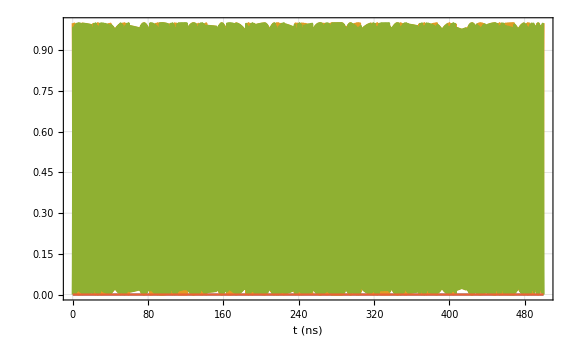
Grid[{-Graphics-,-Graphics-}]

```mathematica
ρ[500,H,Rt,h1,h2,sub]
```

```mathematica
Export["timeEvo_noise.png",p2,ImageResolution->1000]
```

timeEvo_noise.png

```mathematica
H=({{-w, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, w}})+Vdd*({{Cos[x]^2, Cos[x]*Sin[x], Cos[x]*Sin[x], Sin[x]^2}, {Cos[x]*Sin[x], Cos[x]^2, Sin[x]^2, -Cos[x]*Sin[x]}, {Cos[x]*Sin[x], Sin[x]^2, Cos[x]^2, -Cos[x]*Sin[x]}, {Sin[x]^2, -Cos[x]*Sin[x], -Cos[x]*Sin[x], Cos[x]^2}})
Rt=Eigenvectors[H]//Transpose//Simplify
En=Diagonal[Inverse[Rt].H.Rt]//Simplify;
Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}];
hn1=Diagonal[Inverse[Rt].h1.Rt]//Simplify;
hn2=Diagonal[Inverse[Rt].h2.Rt]//Simplify;
Γsquared=Table[hn1[[j]]-hn1[[k]],{j,4},{k,4}]^2+Table[hn2[[j]]-hn2[[k]],{j,4},{k,4}]^2;
ρ0=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Cab[a_,b_]:=KroneckerProduct[Rt[[a,;;]],Transpose[Inverse[Rt]][[b,;;]]]*(Inverse[Rt].ρ0.Rt)
Cab[2,2]
rho=Table[Total[Cab[j,k]*Exp[-J[t]*Γsquared],2],{j,4},{k,4}];
(rhoequil=Table[Total[Cab[j,k]*Table[If[Γsquared[[p,q]]===0,1,0],{p,4},{q,4}],2],{j,4},{k,4}])//.sub
```

(Vdd cos^2(x)-w | Vdd sin(x) cos(x) | Vdd sin(x) cos(x) | Vdd sin^2(x)
Vdd sin(x) cos(x) | Vdd cos^2(x) | Vdd sin^2(x) | -Vdd sin(x) cos(x)
Vdd sin(x) cos(x) | Vdd sin^2(x) | Vdd cos^2(x) | -Vdd sin(x) cos(x)
Vdd sin^2(x) | -Vdd sin(x) cos(x) | -Vdd sin(x) cos(x) | Vdd cos^2(x)+w)

(1 | 0 | -(csc^2(x) (Vdd^3 (-cos(2 x))+Vdd^3 cos(6 x)+2 Vdd^3-Vdd^2 cos(4 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd+8 w)+√2 Vdd^2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 √2 w^2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+8 Vdd^2 w+16 w^3))/(4 Vdd (√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 (-cos(4 x))+Vdd^2+4 w^2)) | (csc^2(x) (Vdd^3 (-cos(2 x))+Vdd^3 cos(6 x)+2 Vdd^3+Vdd^2 cos(4 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd-8 w)-√2 Vdd^2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 √2 w^2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+8 Vdd^2 w+16 w^3))/(4 Vdd (√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-Vdd^2-4 w^2))
(w csc(2 x))/Vdd | -1 | (cot(x) (√2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd^2 cos(4 x)+2 Vdd^2+2 Vdd w cos(2 x)-2 Vdd w+4 w^2))/(√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 (-cos(4 x))+Vdd^2+4 w^2) | (cot(x) (√2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd^2 cos(4 x)-2 Vdd^2-2 Vdd w cos(2 x)+2 Vdd w-4 w^2))/(√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-Vdd^2-4 w^2)
(w csc(2 x))/Vdd | 1 | (cot(x) (√2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-2 Vdd^2 cos(4 x)+2 Vdd^2+2 Vdd w cos(2 x)-2 Vdd w+4 w^2))/(√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 (-cos(4 x))+Vdd^2+4 w^2) | (cot(x) (√2 w √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+2 Vdd^2 cos(4 x)-2 Vdd^2-2 Vdd w cos(2 x)+2 Vdd w-4 w^2))/(√2 Vdd cos(2 x) √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+√2 Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+Vdd^2 cos(4 x)-Vdd^2-4 w^2)
1 | 0 | 1 | 1)

(1)
 |  |  |  |

(0.000155495 | -0.00442891 | -0.00442891 | 0.0000785542
-0.00442891 | 0.499843 | -0.000157081 | -0.00442888
-0.00442891 | -0.000157081 | 0.499843 | -0.00442888
0.0000785542 | -0.00442888 | -0.00442888 | 0.000158668)

```mathematica
J[t_]:=(2-EulerGamma-Log[2π*10^-9*t])/(2*Log[10^12])*t^2;
Ft=Diagonal[(rho-rhoequil)]
```

1
 |  |  |  |

```mathematica
Ft[[2]]//.sub
```

1.2338×10^-8 ⅇ^(-0.000609711 t^2 (-log((π t)/500000000)-ℽ+2))+0.0000801212 ⅇ^(-0.000191607 t^2 (-log((π t)/500000000)-ℽ+2))+0.0000801464 ⅇ^(-0.00016499 t^2 (-log((π t)/500000000)-ℽ+2))+0.0000769719 ⅇ^(-0.000140363 t^2 (-log((π t)/500000000)-ℽ+2))+0.0000769477 ⅇ^(-0.000117725 t^2 (-log((π t)/500000000)-ℽ+2))+0.499843 ⅇ^(-9.94761×10^-7 t^2 (-log((π t)/500000000)-ℽ+2))

```mathematica
T=Solve[(Ft[[2]]//.sub)==Exp[-1],t]
```

$Aborted

```mathematica
Manipulate[
Plot[Ft[[2]]//.{x-> ArcTan[-ϵ,Vt],wn1->wn,wn2->wn,wn-> 0.323,Vdd->0.3,w-> √(ϵ^2+Vt^2),Vt-> 11.4,hx->1,hz->1},{t,0,1000},PlotRange->{0,0.5}],
{ϵ,0,5}]
```

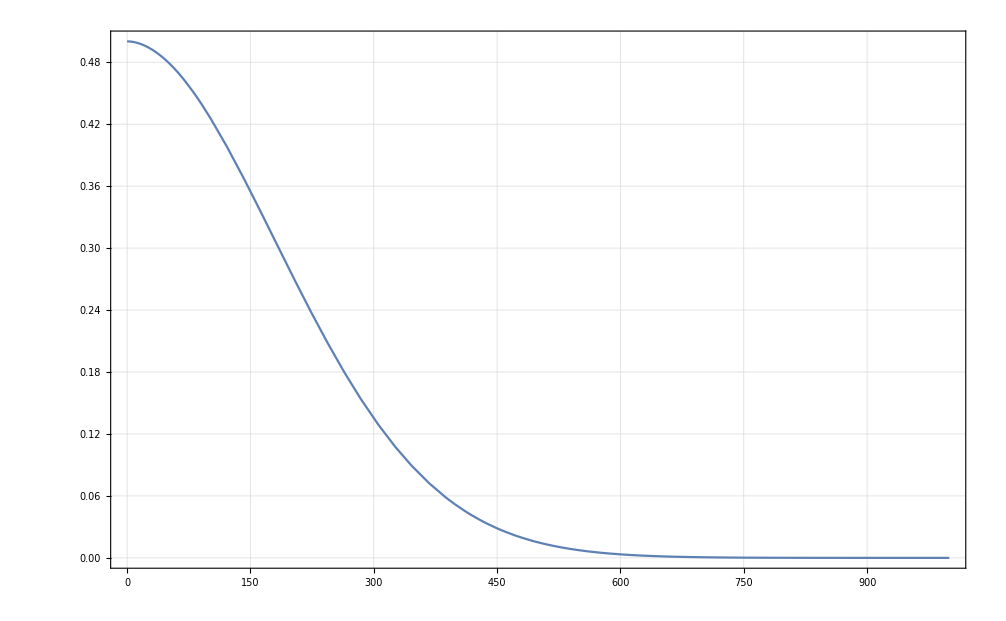

```mathematica
Plot[Abs[Ft[[2]]],{t,0,1000},PlotRange->All,Frame->True,GridLines->Automatic]
```

```mathematica
H=({{-w, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, w}})+Vdd*({{Cos[x]^2, Cos[x]*Sin[x], Cos[x]*Sin[x], Sin[x]^2}, {Cos[x]*Sin[x], Cos[x]^2, Sin[x]^2, -Cos[x]*Sin[x]}, {Cos[x]*Sin[x], Sin[x]^2, Cos[x]^2, -Cos[x]*Sin[x]}, {Sin[x]^2, -Cos[x]*Sin[x], -Cos[x]*Sin[x], Cos[x]^2}})//.{x-> ArcTan[-ϵ,Vt],ϵ->0}
Rt=Eigenvectors[H]//Transpose
En=Diagonal[Inverse[Rt].H.Rt]//Simplify;
Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}]
hn1=Diagonal[Inverse[Rt].h1.Rt]//Simplify;
hn2=Diagonal[Inverse[Rt].h2.Rt]//Simplify;
Γsquared=Table[hn1[[j]]-hn1[[k]],{j,4},{k,4}]^2+Table[hn2[[j]]-hn2[[k]],{j,4},{k,4}]^2
ρ0=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Cab[a_,b_]:=KroneckerProduct[Rt[[a,;;]],Transpose[Inverse[Rt]][[b,;;]]]*(Inverse[Rt].ρ0.Rt)
Cab[2,2]
```

(-w | 0 | 0 | Vdd
0 | 0 | Vdd | 0
0 | Vdd | 0 | 0
Vdd | 0 | 0 | w)

(0 | 0 | -(√(Vdd^2+w^2)+w)/Vdd | -(w-√(Vdd^2+w^2))/Vdd
-1 | 1 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 1 | 1)

(0 | -2 Vdd | √(Vdd^2+w^2)-Vdd | -√(Vdd^2+w^2)-Vdd
2 Vdd | 0 | √(Vdd^2+w^2)+Vdd | Vdd-√(Vdd^2+w^2)
Vdd-√(Vdd^2+w^2) | -√(Vdd^2+w^2)-Vdd | 0 | -2 √(Vdd^2+w^2)
√(Vdd^2+w^2)+Vdd | √(Vdd^2+w^2)-Vdd | 2 √(Vdd^2+w^2) | 0)

(0 | 0 | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2))
0 | 0 | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2))
(hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | 0 | (hz^2 w^2 wn1^2 cos^2(x))/(Vdd^2+w^2)+(hz^2 w^2 wn2^2 cos^2(x))/(Vdd^2+w^2)
(hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | (hz^2 w^2 wn1^2 cos^2(x))/(4 (Vdd^2+w^2))+(hz^2 w^2 wn2^2 cos^2(x))/(4 (Vdd^2+w^2)) | (hz^2 w^2 wn1^2 cos^2(x))/(Vdd^2+w^2)+(hz^2 w^2 wn2^2 cos^2(x))/(Vdd^2+w^2) | 0)

(1/4 | 1/4 | 0 | 0
1/4 | 1/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Γsquared==0
Ones=Table[If[Γsquared[[j,k]]===0,0,1],{j,4},{k,4}]
```

(0 | (16 hx^2 Vdd^2 w^2 wn1^2 sin^4(x) cos^2(x))/((Vdd^2 cos(4 x)-Vdd^2-2 w^2)^2)+(16 hx^2 Vdd^2 w^2 wn2^2 sin^4(x) cos^2(x))/((Vdd^2 cos(4 x)-Vdd^2-2 w^2)^2) | (-(w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(4 hx Vdd w wn1 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2+(-(w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(4 hx Vdd w wn2 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2 | ((w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(4 hx Vdd w wn1 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2+((w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(4 hx Vdd w wn2 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2
(16 hx^2 Vdd^2 w^2 wn1^2 sin^4(x) cos^2(x))/((Vdd^2 cos(4 x)-Vdd^2-2 w^2)^2)+(16 hx^2 Vdd^2 w^2 wn2^2 sin^4(x) cos^2(x))/((Vdd^2 cos(4 x)-Vdd^2-2 w^2)^2) | 0 | (w^2 wn1^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2)+(w^2 wn2^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2) | (w^2 wn1^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2)+(w^2 wn2^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2)
((w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))+(4 hx Vdd w wn1 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2+((w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))+(4 hx Vdd w wn2 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2))^2 | (w^2 wn1^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2)+(w^2 wn2^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2) | 0 | ((w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))+(w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2+((w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))+(w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2
((4 hx Vdd w wn1 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2)-(w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2+((4 hx Vdd w wn2 sin^2(x) cos(x))/(Vdd^2 cos(4 x)-Vdd^2-2 w^2)-(w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2 | (w^2 wn1^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2)+(w^2 wn2^2 cos^2(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2)^2)/(2 (-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)^2) | (-(w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(w wn1 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2+(-(w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)+hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)-4 Vdd)-√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2))-(w wn2 cos(x) (Vdd^2 (hx-2 hz) cos(4 x)-hx Vdd cos(2 x) (√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+4 Vdd)+√2 hx Vdd √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2)+3 hx Vdd^2+2 hz Vdd^2+4 hz w^2))/(√2 √(-4 Vdd^2 cos(2 x)-3 Vdd^2 cos(4 x)+7 Vdd^2+8 w^2) (Vdd^2 (-cos(4 x))+Vdd^2+2 w^2)))^2 | 0)==0

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
Q[ϵ_,Vt_]:=Abs[(ϵ^2+Vt^2)/(√2 wn*ϵ)]//.{wn->0.323}
```

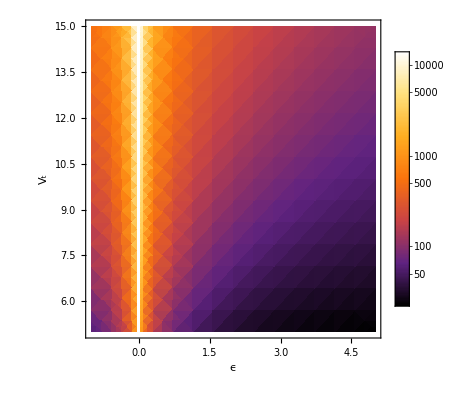

```mathematica
p=DensityPlot[Q[x,y],{x,-1,5},{y,5,15},PlotLegends->Automatic,ScalingFunctions->"Log10",ColorFunction->"SunsetColors",Frame->True,FrameLabel->{"ϵ","V_t"}]
```

```mathematica
Export["chargeQuality.png",p,ImageResolution->500]
```

chargeQuality.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["chargeQuality.png"]]]
```